```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\Saccharide\\Standard.xlsx"]
```

{{{0.,0.},{0.00444444,0.121},{0.00888889,0.345},{0.0133333,0.572},{0.0177778,0.817},{0.0222222,1.032}}}

```mathematica
data={{0.,0.},{0.004444444444444445,0.121},{0.00888888888888889,0.345},{0.013333333333333332,0.572},{0.01777777777777778,0.817},{0.022222222222222223,1.032}}
```

{{0.,0.},{0.00444444,0.121},{0.00888889,0.345},{0.0133333,0.572},{0.0177778,0.817},{0.0222222,1.032}}

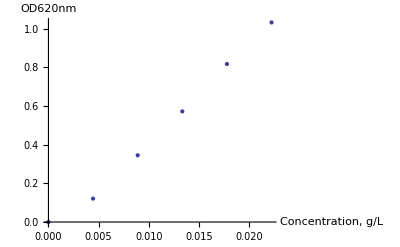

```mathematica
gra=ListPlot[data,AxesLabel->{"Concentration, g/L","OD620nm"}]
```

```mathematica
gra2=LinearModelFit[data,x,x]
```

```mathematica
Normal[gra2]
```

-0.0527619+48.0536 x

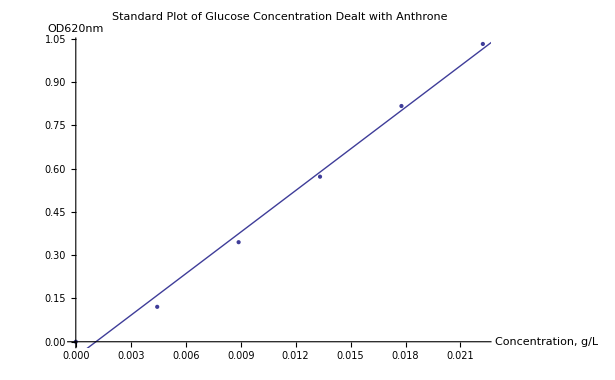

```mathematica
Show[gra,Plot[gra2[x],{x,0,0.25}],PlotLabel->"Standard Plot of Glucose Concentration Dealt with Anthrone"]
```

```mathematica
gra2["RSquared"]
```

0.992525

```mathematica
Solve[y==-0.05276190476190524+48.053571428571445 x,x]
```

{{x→-0.0208101 (-0.0527619-y)}}

```mathematica
a[b_]=-0.020810107766629497 (-0.05276190476190524-b);
a[0.408]
```

0.0095885

```mathematica
a[0.807]
```

0.0178917

```mathematica
data3={{0.0095885,0.408},{0.0178917,0.807}}
```

{{0.0095885,0.408},{0.0178917,0.807}}

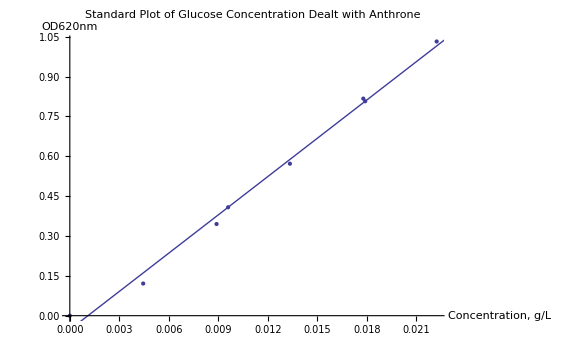

```mathematica
Show[gra,Plot[gra2[x],{x,0,0.25}],ListPlot[data3],PlotLabel->"Standard Plot of Glucose Concentration Dealt with Anthrone"]
```